# Motorbike net2 & net3

## Set Environment

```mathematica
home = "/home/lichao/scratch/pami/";workdir = "/home/lichao/git/geonb/";SetDirectory[workdir];
```

```mathematica
prefix = "quad_train_";
```

```mathematica
Needs["Posecpp`","posecpp_network.wl"];
```

## Generate Network 2

### load raw data

```mathematica
rawData=LoadNetwork2Raw[home<>"motor_net2_raw.txt"];rawData//Dimensions
```

{80177,8}

```mathematica
rawData=LoadNetwork2Raw[home<>prefix<>"net2_raw.txt"];rawData//Dimensions
```

{320231,8}

### find best threshold

```mathematica
Module[{n = 500,v=2,a},a =ConstructNetwork2[rawData,n,v];Sow[Length[a]];
Complement[a,ConstructNetwork2[rawData,n,v-0.1]]]//Reap;
```

```mathematica
el2 = ConstructNetwork2[rawData,500,2];g2 = Graph[el2,VertexLabels->"Name"];
```

```mathematica
VertexCount[g2]
EdgeCount[g2]
```

449

2055

### Node Research

```mathematica
Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]]
```

{346,378,356,220,251,379,72,250,168,162,14,148,56,268,111,135,288,312,344,241,260,54,40,156,169,271,21,144,66,130,46,256,36,15,296,84,26,380,328,133,105,45,33,210,150,191,174,119,69,231,198,93,47,29,176,51,206,149,64,41,16,3,316,345,301,209,182,177,163,147,129,370,83,61,30,22,5,0,299,286,278,365,240,238,236,320,315,211,203,195,180,155,153,273,146,109,82,63,62,55,38,31,368,137,73,6,4,2,342,335,327,302,267,258,237,235,230,222,364,215,214,205,161,157,145,142,126,124,118,117,376,100,97,80,67,57,343,332,323,322,319,300,297,294,291,285,284,257,242,228,224,193,186,173,166,262,204,187,385,140,136,122,106,85,75,68,53,35,34,32,12,10,7,369,352,349,347,334,325,309,305,304,292,287,283,281,249,247,246,234,208,207,199,197,196,188,184,179,178,175,165,225,160,139,112,110,103,102,99,96,90,79,77,74,60,59,128,52,43,24,23,361,359,354,338,336,333,330,318,314,313,307,306,298,295,293,289,275,274,270,269,263,261,255,254,252,243,233,227,389,218,217,216,213,202,201,171,167,351,340,158,154,141,138,132,121,116,115,107,98,94,92,89,88,86,78,76,71,65,49,48,42,37,28,20,19,18,9}

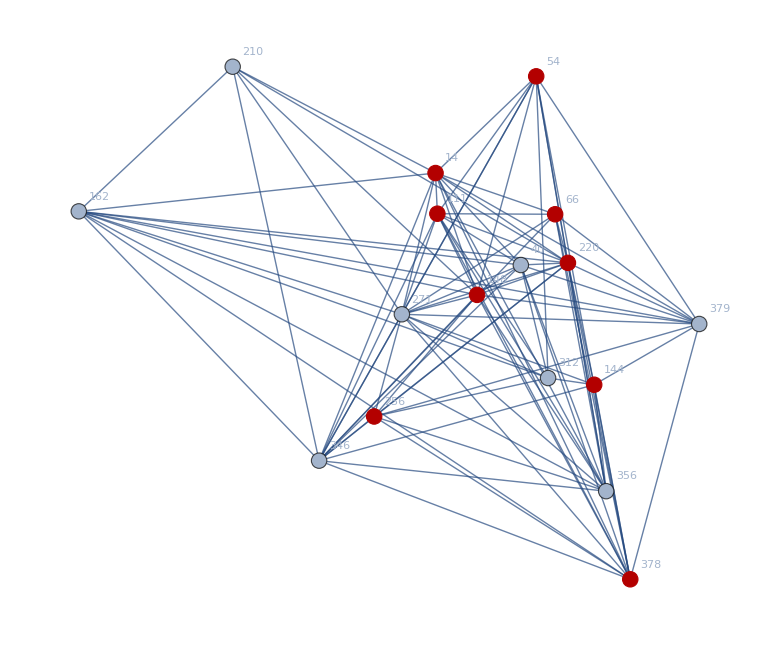

```mathematica
HighlightGraph[NeighborhoodGraph[g2,271,VertexLabels->"Name"],VertexList[g3]]
```

### Export Graph

```mathematica
Export["quad_train_net2_el.txt",EdgeList[g2]]
```

quad_train_net2_el.txt

## Load Network 3

### read Edge List

```mathematica
el3=LoadNetwork3[home<>"quad_train_net3_el_02_02.txt"]
```

{0<->222,0<->273,1<->347,1<->538,2<->144,2<->249,14<->349,19<->203,19<->306,24<->83,26<->306,32<->485,38<->278,38<->491,51<->81,51<->239,51<->290,51<->508,51<->636,61<->395,62<->187,65<->284,69<->126,69<->154,70<->230,85<->156,93<->214,98<->554,107<->144,107<->153,107<->468,109<->347,111<->167,114<->333,118<->212,118<->370,126<->153,126<->154,128<->483,137<->200,137<->232,144<->153,144<->298,145<->333,153<->231,155<->209,156<->268,163<->252,166<->613,174<->179,174<->474,178<->452,203<->218,203<->483,203<->632,209<->300,212<->311,212<->365,214<->512,218<->280,218<->306,218<->434,222<->424,222<->555,225<->311,225<->347,231<->315,239<->406,239<->508,249<->468,250<->326,258<->292,267<->406,280<->306,298<->554,300<->312,308<->661,311<->365,312<->534,321<->360,326<->555,327<->636,328<->399,338<->399,347<->538,347<->597,364<->485,365<->370,365<->485,383<->434,387<->434,397<->399,397<->451,402<->498,410<->593,416<->419,424<->555,431<->452,446<->642,464<->632,471<->643,486<->634,508<->636,566<->635,593<->642,725<->793}

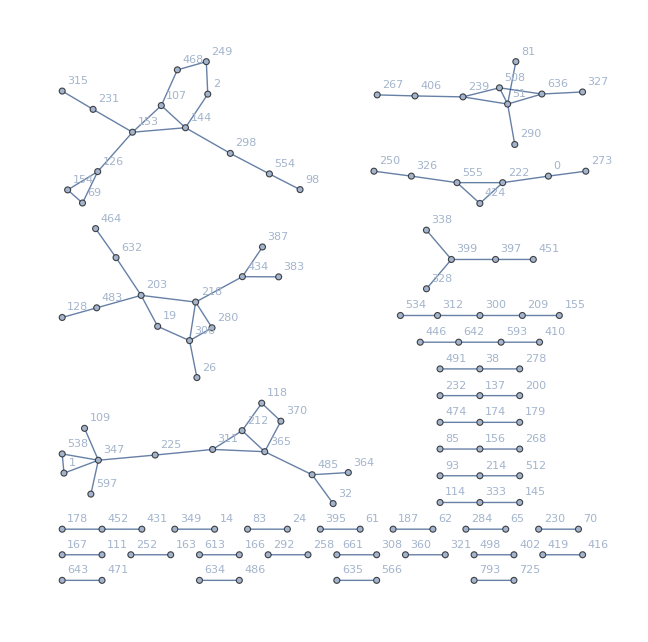

```mathematica
g3=Graph[el3,VertexLabels->"Name"]
```

```mathematica
VertexList[g3]//Sort
```

{0,3,7,14,15,16,21,22,26,31,32,33,34,35,36,45,46,47,54,55,56,61,62,63,64,66,67,69,72,73,75,83,84,85,90,93,97,99,100,103,105,109,111,117,118,119,122,124,126,129,130,136,140,142,144,147,148,149,155,156,157,163,165,168,169,175,176,177,179,180,182,193,195,196,198,199,203,206,208,211,214,220,222,230,231,237,238,240,242,246,251,256,257,258,260,267,278,281,283,284,287,288,291,292,296,299,302,304,305,309,319,322,323,325,327,332,343,345,347,352,369,376,378}

```mathematica
comp3=ConnectedComponents[Graph[el3]]
```

{{249,2,468,144,107,153,298,126,231,554,69,154,315,98},{32,485,364,365,212,311,370,118,225,347,1,109,538,597},{383,434,218,387,203,280,306,19,483,632,26,128,464},{81,51,239,290,508,636,406,327,267},{250,326,555,222,424,0,273},{534,312,300,209,155},{338,399,328,397,451},{642,446,593,410},{431,452,178},{214,93,512},{268,156,85},{232,137,200},{38,278,491},{474,174,179},{145,333,114},{258,292},{163,252},{65,284},{793,725},{24,83},{634,486},{167,111},{308,661},{566,635},{613,166},{360,321},{70,230},{402,498},{395,61},{62,187},{643,471},{349,14},{416,419}}

## Load Global data

```mathematica
{gx,gy,gs,gn}=LoadGlobalData[home<>prefix<>"converge_x.txt",home<>prefix<>"converge_y.txt",home<>prefix<>"converge_s.txt",home<>prefix<>"converge_n.txt"];
```

```mathematica
cx = gx+gs/2;cy=-(gy+gs/2);
```

```mathematica
cx;
```

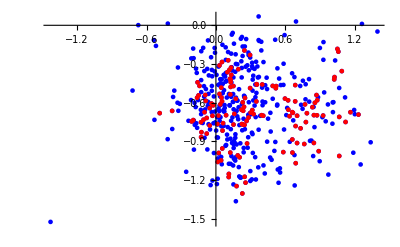

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,{Keys[gx],VertexList[g3]},{2}],PlotStyle->{Blue,Red}]
```

```mathematica
Export[home<>prefix<>"global_summary.txt",Map[{#,gx[#],gy[#],gs[#]}&,Keys[gx]]]
```

/home/lichao/scratch/pami/quad_train_global_summary.txt

```mathematica
Intersection[#,Keys[gx]]&/@comp3
```

{{2,69,98,107,126,144,153,154,231,249,298,315,468,554},{1,32,109,118,212,225,311,347,364,365,370,485,538,597},{19,26,128,203,218,280,306,383,387,434,464,483,632},{51,81,239,267,290,327,406,508,636},{0,222,250,273,326,424,555},{155,209,300,312,534},{328,338,397,399,451},{410,446,593,642},{178,431,452},{93,214,512},{85,156,268},{137,200,232},{38,278,491},{174,179,474},{114,145,333},{258,292},{163,252},{65,284},{725,793},{24,83},{486,634},{111,167},{308,661},{566,635},{166,613},{321,360},{70,230},{402,498},{61,395},{62,187},{471,643},{14,349},{416,419}}

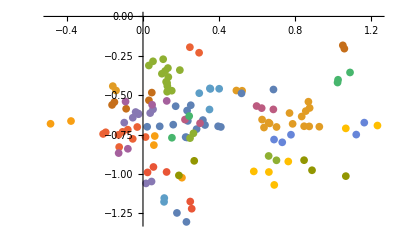

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,Intersection[#,Keys[gx]]&/@comp3,{2}]]
```

```mathematica
ListPointPlot3D[Map[{cx[#],cy[#],gs[#]}&,Intersection[#,Keys[gx]]&/@comp3,{2}],Filling->Bottom,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
Mean[gs]
```

0.417891

```mathematica
StandardDeviation[gs]
```

0.130251

```mathematica
Mean/@Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{0.360756,0.344439,0.362133,0.38136,0.352032,0.396469,0.767527,0.3965,0.372281,0.330848,0.836027,0.366872,0.475844,0.335979,0.410927,0.412599,0.766951,0.674244}

```mathematica
Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{{0.354006,0.361811,0.358521,0.341208,0.368141,0.380846},{0.330545,0.34774,0.342344,0.362643,0.338923},{0.374262,0.34284,0.363975,0.367456},{0.381039,0.389704,0.373338},{0.346285,0.357779},{0.39348,0.399458},{0.813928,0.721127},{0.38905,0.403949},{0.376815,0.367747},{0.334944,0.326751},{0.755648,0.916406},{0.370876,0.362867},{0.456433,0.495254},{0.333575,0.338383},{0.412666,0.409188},{0.407534,0.417664},{0.837074,0.696827},{0.785451,0.563036}}

```mathematica
sOrderByD = gs[#]&/@Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]];
```

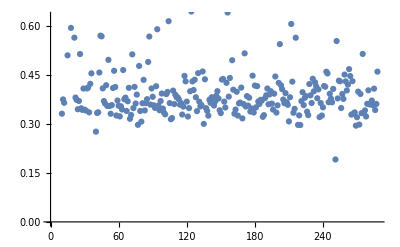

```mathematica
ListPlot[sOrderByD]
```

```mathematica
sOrderByP = gs[#]&/@Part[VertexList[g2],Ordering[PageRankCentrality[g2,0.1],All,Greater]];
```

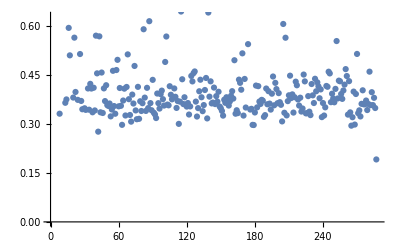

```mathematica
ListPlot[sOrderByP]
```

## Scale Slice

```mathematica
sLayers =SLayer[Keys[gx],gs]
```

<|6→{0,9,12,33,51,80,84,86,111,117,140,141,198,225,255,261,271,320,345,351,370},5→{2,7,14,20,22,23,31,35,36,37,40,49,54,57,61,63,64,66,69,77,82,85,89,90,94,103,112,121,124,126,136,138,139,142,145,153,154,158,160,161,163,165,166,167,169,171,174,176,177,179,184,187,191,193,195,197,199,202,203,204,206,208,209,213,216,222,224,227,234,236,243,246,252,256,257,263,267,269,281,283,284,285,291,293,295,296,297,298,300,301,302,304,306,307,309,313,318,322,327,330,334,335,338,340,352,354,361,364,365,368},4→{3,4,6,10,15,16,18,19,21,28,29,30,32,34,38,41,42,43,45,46,47,48,53,55,60,62,65,68,71,73,74,75,76,78,83,88,93,96,97,98,99,100,102,105,106,109,110,115,116,118,119,122,129,130,132,144,146,147,148,149,155,156,162,173,175,178,180,182,186,188,196,201,205,207,211,214,215,228,230,231,233,235,237,238,240,242,247,249,254,258,270,274,275,278,286,287,289,292,294,299,305,314,316,319,323,325,332,333,336,342,343,347,349,359,369,376},3→{5,24,52,67,92,107,133},8→{26,168,251,268,288,378,379,380,385},9→{56,72,128,135,328,344,356},7→{59,79,137,150,157,210,217,220,241,260,262,273,312,315,389},1→{218},10→{250,346}|>

```mathematica
ListPointPlot3D[Map[{cx[#],cy[#],gs[#]}&,Keys[gx]],Filling->Bottom,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
DeleteCases[Intersection[#,sLayers[4]]&/@comp3,{}]
```

{{93,119,211,242},{47,83,144,278,299},{130,148,376},{62,99},{292},{15,129},{238},{55,118}}

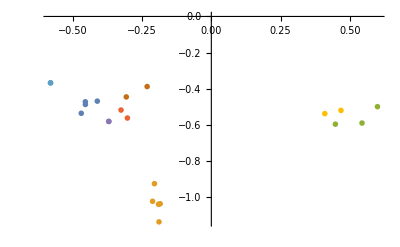

```mathematica
Module[{pos,idx},idx=DeleteCases[Intersection[#,sLayers[4]]&/@comp3,{}];pos=Map[{cx[#],cy[#]}&,idx,{2}];ListPlot[pos,PlotMarkers->idx]]
```

```mathematica
Export["ScaleLayer_"<>ToString[#]<>".pdf",SLayerPlot[#,sLayers,cx,cy]]&/@Keys[sLayers]
```

{ScaleLayer_6.pdf,ScaleLayer_5.pdf,ScaleLayer_4.pdf,ScaleLayer_3.pdf,ScaleLayer_8.pdf,ScaleLayer_9.pdf,ScaleLayer_7.pdf,ScaleLayer_1.pdf,ScaleLayer_10.pdf}

```mathematica
Directory
```

Directory

```mathematica
gall = Association[Map[#->{cx[#],cy[#],gs[#]}&,Keys[gx]]];
```

```mathematica
gall[0]
```

{0.111907,0.762903,0.476548}

```mathematica
SLayerPlot[1,sLayers,cx,cy]
```

SLayerPlot[1,<|6→{0,9,12,33,51,80,84,86,111,117,140,141,198,225,255,261,271,320,345,351,370},5→{2,7,14,20,22,23,31,35,36,37,40,49,54,57,61,63,64,66,69,77,82,85,89,90,94,103,112,121,124,126,136,138,139,142,145,153,154,158,160,161,163,165,166,167,169,171,174,176,177,179,184,187,191,193,195,197,199,202,203,204,206,208,209,213,216,222,224,227,234,236,243,246,252,256,257,263,267,269,281,283,284,285,291,293,295,296,297,298,300,301,302,304,306,307,309,313,318,322,327,330,334,335,338,340,352,354,361,364,365,368},4→{3,4,6,10,15,16,18,19,21,28,29,30,32,34,38,41,42,43,45,46,47,48,53,55,60,62,65,68,71,73,74,75,76,78,83,88,93,96,97,98,99,100,102,105,106,109,110,115,116,118,119,122,129,130,132,144,146,147,148,149,155,156,162,173,175,178,180,182,186,188,196,201,205,207,211,214,215,228,230,231,233,235,237,238,240,242,247,249,254,258,270,274,275,278,286,287,289,292,294,299,305,314,316,319,323,325,332,333,336,342,343,347,349,359,369,376},3→{5,24,52,67,92,107,133},8→{26,168,251,268,288,378,379,380,385},9→{56,72,128,135,328,344,356},7→{59,79,137,150,157,210,217,220,241,260,262,273,312,315,389},1→{218},10→{250,346}|>,cx,cy]

```mathematica
Manipulate[SLayerPlot[x,sLayers,cx,cy],{x,1,10,1}]
```

## Voronoi Centers for part

```mathematica
defined =Keys[gx];
```

```mathematica
voroComms= Intersection[defined,#]&/@Select[comp3,Length[#]>2&]
```

{{2,69,98,107,126,144,153,154,231,249,298,315,468,554},{1,32,109,118,212,225,311,347,364,365,370,485,538,597},{19,26,128,203,218,280,306,383,387,434,464,483,632},{51,81,239,267,290,327,406,508,636},{0,222,250,273,326,424,555},{155,209,300,312,534},{328,338,397,399,451},{410,446,593,642},{178,431,452},{93,214,512},{85,156,268},{137,200,232},{38,278,491},{174,179,474},{114,145,333}}

```mathematica
centers =Mean/@Map[{gx[#],gy[#],gs[#]}&,voroComms,{2}]
```

{{0.0657764,0.504211,0.345896},{0.58569,0.45963,0.390463},{-0.0540444,0.203026,0.341755},{-0.273054,0.580206,0.342325},{-0.19579,0.449031,0.349426},{-0.22584,0.380651,0.322221},{0.129655,0.270102,0.441721},{0.507635,0.823951,0.334096},{-0.213754,0.305203,0.481651},{0.675642,0.709693,0.516881},{-0.11562,0.794978,0.3666},{0.570881,0.615348,0.324462},{-0.0493837,0.709708,0.314708},{0.470828,0.415839,0.329564},{0.886292,0.233099,0.318887}}

```mathematica
ListPointPlot3D[centers]
```

-Graphics3D-

```mathematica
Length[centers]
```

22

```mathematica
Export[home<>prefix<>"voro_centers.txt",centers]
```

/home/lichao/scratch/pami/quad_train_voro_centers.txt